# Simulating Different Rules For a Four-Way Intersection

Hyun Min Kim

Mentor: Sylvia Haas

### Project Description

The project I will work on will be primarily determining various rules for a four-way intersection and determining the level of efficiency each provides to various types of traffic flow. The project will involve creating a simulation where vehicles interact with each other in the intersection. Each rule will be simulated for the efficiency by various intervals in which they arrive in an intersection. The primary goal of this project is to find the set of the most efficient rules for all of the different types of traffic flow on average.

### Intersection Set Up

#### Variables

Lines and a global variable

```mathematica
hLines = {Line[{{-11,0},{11,0}}]};
```

```mathematica
vLines = {Line[{{0,-11},{0,11}}]};
```

```mathematica
waffle = True;
```

#### Rule 184 in traffic

Cellular Automata 184 resembles traffic flow in a rightward direction.

```mathematica
Animate[CellularAutomaton[184,{1,0,1,0,0,0,1,1,1,1},10][[n]],{n,1,11,1}]
```

#### Random Car List Generation

These two functions generate cars at random spots behinds the intersection at the x and the y axis.

```mathematica
randCarLineX[numCar_Integer,space_Integer]:=RandomChoice/@MapThread[List,{{Join[MapThread[Style,{Point/@MapThread[List,{Range[-(numCar+space)/2,-(numCar+space)/2+numCar-1],Table[0,numCar]}],Table[RandomColor[],numCar]}],Table[0,space]]}//Flatten,Table[0,numCar+space]}]
```

```mathematica
randCarLineY[numCar_Integer,space_Integer]:=RandomChoice/@MapThread[List,{{Join[MapThread[Style,{Point/@MapThread[List,{Table[0,numCar],Range[-(numCar+space)/2,-(numCar+space)/2+numCar-1]}],Table[RandomColor[],numCar]}],Table[0,space]]}//Flatten,Table[0,numCar+space]}]
```

#### Intersection and stop sign check functions

These functions check and store cars in the intersection and the stop sign

```mathematica
isInIntersection[point_Point]:= If[point[[1,1]]<2&&point[[1,1]]>-2&&point[[1,2]]<2&&point[[1,2]]>-2, True,False]
```

```mathematica
isAtStopSign[point_Point]:=If[(point[[1,1]]==-2&&point[[1,2]]==0)||(point[[1,1]]==0&&point[[1,2]]==-2),True, False]
```

```mathematica
checkStop[list_]:=(
carsAtStopSign = Append[carsAtStopSign,Select[Select[list,!IntegerQ[#]&],isAtStopSign[#[[1]]]&]]//Flatten
)
```

```mathematica
checkIntersection[list_]:=(
carsInIntersection = Append[carsInIntersection,Select[Select[list,!IntegerQ[#]&],isInIntersection[#[[1]]]&]]//Flatten
)
```

### Implementing Intersection Rules

#### Rule #1 -> Yield for traffic

Function with rules of the Y-Axis cars yielding for X-Axis’ cars, one for taking in lists, and the other retrieving cars by interval.

Checks if car is at the end of the road and updates carCount

Performs calculations based on cars in the intersection and at the stop sign

Iterates Rule 184 behind intersection

Moves the cars which are past and in intersection

```mathematica
roadRule[listX_,listY_,carsBehindStop_]:=(
  cloneX = listX;
cloneY = listY;
iterationCount++;
carsAtStopSign = {};
carsInIntersection = {};
checkStop[listX];
checkStop[listY];
checkIntersection[listX];
checkIntersection[listY];
If[!IntegerQ[cloneX[[-1]]],carCount++];
If[!IntegerQ[cloneY[[-1]]],carCount++];
If[!IntegerQ[cloneX[[carsBehindStop +1]]],changeLaterX = True, changeLaterX = False];
cloneX = Join[Take[cloneX,carsBehindStop+1],Take[cloneX,{carsBehindStop+1,Length[cloneX]-1}]] ;
MapIndexed[If[First[#2]>carsBehindStop&&!NumberQ[cloneX[[First[#2]]]],cloneX[[First[#2],1,1,1]]++]&,cloneX];
If[!IntegerQ[cloneY[[carsBehindStop +1]]],changeLaterY = True, changeLaterY = False];
cloneY = Join[Take[cloneY,carsBehindStop+1],Take[cloneY,{carsBehindStop+1,Length[cloneY]-1}]] ;
MapIndexed[If[First[#2]>carsBehindStop&&!NumberQ[cloneY[[First[#2]]]],cloneY[[First[#2],1,1,2]]++]&,cloneY];
If[Length[carsInIntersection]==0,If[Length[carsAtStopSign]≠0,If[Length[carsAtStopSign ]==1,If[carsAtStopSign[[1,1,1,2]]==0,cloneX[[carsBehindStop+1]]=listX[[carsBehindStop]];cloneX[[carsBehindStop]]=0;cloneX[[carsBehindStop+1,1,1,1]]++;,
cloneY[[carsBehindStop+1]]=listY[[carsBehindStop]];cloneY[[carsBehindStop+1,1,1,2]]++;cloneY[[carsBehindStop]]=0;],If[cloneX[[carsBehindStop+1]]=listX[[carsBehindStop]];cloneX[[carsBehindStop]]=0;cloneX[[carsBehindStop+1,1,1,1]]++;,cloneY[[carsBehindStop+1]]=listY[[carsBehindStop]];cloneY[[carsBehindStop+1,1,1,2]]++;cloneY[[carsBehindStop]]=0;];]]
];
For[i=carsBehindStop,i> 1,i--,
If[NumberQ[listX[[i]]]&&!NumberQ[listX[[i-1]]],{cloneX[[i]]=listX[[i-1]];cloneX[[i,1,1,1]]++;cloneX[[i-1]]=0},cloneX[[i-1]]=listX[[i-1]]];If[NumberQ[listY[[i]]]&&!NumberQ[listY[[i-1]]],{cloneY[[i]]=listY[[i-1]];cloneY[[i,1,1,2]]++;cloneY[[i-1]]=0},cloneY[[i-1]]=listY[[i-1]]];
];
If[changeLaterX,cloneX[[carsBehindStop+1]]=0];
If[changeLaterY,cloneY[[carsBehindStop+1]]=0];
Return[{cloneX,cloneY}];
;)
```

#### Iterating function for Rule #1

I created a function which iterates through the road rules given the list of cars on the x-axis and the y-axis, the amount of cars possible behind the intersection, and the number of times to iterate.

```mathematica
iterateRule[listX_,listY_,cbs_,times_]:=(
iterationCount=0;
carCount = 0;
NestList[roadRule[#[[1]],#[[2]],cbs]&,{listX,listY},times])
```

#### Visualizing Rule #1

Using the randCar functions, I generated random roads with cars as points.

```mathematica
xAxis = randCarLineX[10,12]
```

{0,Point[{-10,0}],0,0,Point[{-7,0}],0,Point[{-5,0}],0,Point[{-3,0}],Point[{-2,0}],0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
yAxis = randCarLineY[10,12]
```

{0,Point[{0,-10}],0,Point[{0,-8}],Point[{0,-7}],0,Point[{0,-5}],Point[{0,-4}],0,Point[{0,-2}],0,0,0,0,0,0,0,0,0,0,0,0}

I used the iterating function to generate the state of the road at each iteration for 70 iterations.

```mathematica
iter=iterateRule[xAxis,yAxis,10,70];
```

I plotted each iteration on a graph and created a manipulate to go through the 70 iterations.

```mathematica
Manipulate[Graphics[{PointSize[0.025],Select[(Flatten/@iter)[[n]],!IntegerQ[#]&],hLines[[1]],vLines[[1]]}],{n,1,70,1},SaveDefinitions->True]
```

#### Rule #2 -> Alternate at intersection

Function with rules for both axes to alternate cars at the intersection, rather than having one flow of traffic pass after the other completely passes.

Same basic rules as the yield function(Rule 184 and intersection function)

Traffic “Waffle”(Alternating traffic by a boolean called “waffle”, a term originated by Sylvia Haas)

```mathematica
roadRuleEdit[listX_,listY_,carsBehindStop_]:=(
iterationCount++;
cloneX = listX;
cloneY = listY;
carsAtStopSign = {};
carsInIntersection = {};
checkStop[listX];
checkStop[listY];
checkIntersection[listX];
checkIntersection[listY];
If[!IntegerQ[cloneX[[-1]]],carCount++];
If[!IntegerQ[cloneY[[-1]]],carCount++];
If[!IntegerQ[cloneX[[carsBehindStop +1]]],changeLaterX = True, changeLaterX = False];
cloneX = Join[Take[cloneX,carsBehindStop+1],Take[cloneX,{carsBehindStop+1,Length[cloneX]-1}]] ;
MapIndexed[If[First[#2]>carsBehindStop&&!NumberQ[cloneX[[First[#2]]]],cloneX[[First[#2],1,1,1]]++]&,cloneX];
If[!IntegerQ[cloneY[[carsBehindStop +1]]],changeLaterY = True, changeLaterY = False];
cloneY = Join[Take[cloneY,carsBehindStop+1],Take[cloneY,{carsBehindStop+1,Length[cloneY]-1}]] ;
MapIndexed[If[First[#2]>carsBehindStop&&!NumberQ[cloneY[[First[#2]]]],cloneY[[First[#2],1,1,2]]++]&,cloneY];
If[Length[carsInIntersection]==0,If[Length[carsAtStopSign]≠0,If[Length[carsAtStopSign ]==1,If[carsAtStopSign[[1,1,1,2]]==0,cloneX[[carsBehindStop+1]]=listX[[carsBehindStop]];cloneX[[carsBehindStop]]=0;cloneX[[carsBehindStop+1,1,1,1]]++;,
cloneY[[carsBehindStop+1]]=listY[[carsBehindStop]];cloneY[[carsBehindStop+1,1,1,2]]++;cloneY[[carsBehindStop]]=0;],If[waffle, cloneX[[carsBehindStop+1]]=listX[[carsBehindStop]];cloneX[[carsBehindStop]]=0;cloneX[[carsBehindStop+1,1,1,1]]++;waffle = False,cloneY[[carsBehindStop+1]]=listY[[carsBehindStop]];cloneY[[carsBehindStop+1,1,1,2]]++;cloneY[[carsBehindStop]]=0;waffle = True];]]
];
For[i=carsBehindStop,i> 1,i--,
If[NumberQ[listX[[i]]]&&!NumberQ[listX[[i-1]]],{cloneX[[i]]=listX[[i-1]];cloneX[[i,1,1,1]]++;cloneX[[i-1]]=0},cloneX[[i-1]]=listX[[i-1]]];If[NumberQ[listY[[i]]]&&!NumberQ[listY[[i-1]]],{cloneY[[i]]=listY[[i-1]];cloneY[[i,1,1,2]]++;cloneY[[i-1]]=0},cloneY[[i-1]]=listY[[i-1]]];
];
If[changeLaterX,cloneX[[carsBehindStop+1]]=0];
If[changeLaterY,cloneY[[carsBehindStop+1]]=0];
Return[{cloneX,cloneY}];
)
```

#### Iterating function for Rule #2

I created another similar function which iterates Rule #2

```mathematica
iterateRuleEdit[listX_,listY_,cbs_,times_]:=(
carCount=0;
NestList[roadRuleEdit[#[[1]],#[[2]],cbs]&,{listX,listY},times]
)
```

#### Visualizing Rule #2

I used the same cars in the x-axis and the y-axis and saw how it compared to the yielding function.
I ran the iterate function for Rule #2, just like before...

```mathematica
iterInter = iterateRuleEdit[xAxis,yAxis,10,70];
```

and plotted the iterations on a graph by animate.

```mathematica
Animate[Graphics[{PointSize[0.025],Select[(Flatten/@iterInter)[[n]],!IntegerQ[#]&],hLines[[1]],vLines[[1]]}],{n,1,70,1},SaveDefinitions->True]
```

### Experimenting with continuous traffic flow

Creating a function for a continuous flow of cars

These two functions push cars onto the road at set intervals for both axes.
It uses the mod function to determine the current iteration count and decide whether it is in the set interval.

```mathematica
pushCarX[list_,interval_]:=If[Mod[iterationCount,interval]==0&&IntegerQ[cloneX[[1]]],cloneX[[1]]=Style[Point[{-11,0}],RandomColor[]]]
```

```mathematica
pushCarY[list_,interval_]:=If[Mod[iterationCount,interval]==0&&IntegerQ[cloneY[[1]]],cloneY[[1]]=Style[Point[{0,-11}],RandomColor[]]]
```

#### Incorporating Rule #1

I overloaded the Rule #1 function to have “interval” as one of the parameters. This is the interval for cars being put on the road.
To add cars, I had to use the functions previously created to put cars on the roads.

```mathematica
roadRule[listX_,listY_,carsBehindStop_,interval_]:=(
cloneX = listX;
cloneY = listY;
iterationCount++;
carsAtStopSign = {};
carsInIntersection = {};
checkStop[listX];
checkStop[listY];
checkIntersection[listX];
checkIntersection[listY];
If[!IntegerQ[cloneX[[-1]]],carCount++];
If[!IntegerQ[cloneY[[-1]]],carCount++];
If[!IntegerQ[cloneX[[carsBehindStop +1]]],changeLaterX = True, changeLaterX = False];
cloneX = Join[Take[cloneX,carsBehindStop+1],Take[cloneX,{carsBehindStop+1,Length[cloneX]-1}]] ;
MapIndexed[If[First[#2]>carsBehindStop&&!NumberQ[cloneX[[First[#2]]]],cloneX[[First[#2],1,1,1]]++]&,cloneX];
If[!IntegerQ[cloneY[[carsBehindStop +1]]],changeLaterY = True, changeLaterY = False];
cloneY = Join[Take[cloneY,carsBehindStop+1],Take[cloneY,{carsBehindStop+1,Length[cloneY]-1}]] ;
MapIndexed[If[First[#2]>carsBehindStop&&!NumberQ[cloneY[[First[#2]]]],cloneY[[First[#2],1,1,2]]++]&,cloneY];
If[Length[carsInIntersection]==0,If[Length[carsAtStopSign]≠0,If[Length[carsAtStopSign ]==1,If[carsAtStopSign[[1,1,1,2]]==0,cloneX[[carsBehindStop+1]]=listX[[carsBehindStop]];cloneX[[carsBehindStop]]=0;cloneX[[carsBehindStop+1,1,1,1]]++;,
cloneY[[carsBehindStop+1]]=listY[[carsBehindStop]];cloneY[[carsBehindStop+1,1,1,2]]++;cloneY[[carsBehindStop]]=0;],If[cloneX[[carsBehindStop+1]]=listX[[carsBehindStop]];cloneX[[carsBehindStop]]=0;cloneX[[carsBehindStop+1,1,1,1]]++;,cloneY[[carsBehindStop+1]]=listY[[carsBehindStop]];cloneY[[carsBehindStop+1,1,1,2]]++;cloneY[[carsBehindStop]]=0;];]]
];
For[i=carsBehindStop,i> 1,i--,
If[NumberQ[listX[[i]]]&&!NumberQ[listX[[i-1]]],{cloneX[[i]]=listX[[i-1]];cloneX[[i,1,1,1]]++;cloneX[[i-1]]=0},cloneX[[i-1]]=listX[[i-1]]];If[NumberQ[listY[[i]]]&&!NumberQ[listY[[i-1]]],{cloneY[[i]]=listY[[i-1]];cloneY[[i,1,1,2]]++;cloneY[[i-1]]=0},cloneY[[i-1]]=listY[[i-1]]];
];
If[changeLaterX,cloneX[[carsBehindStop+1]]=0];
If[changeLaterY,cloneY[[carsBehindStop+1]]=0];
pushCarX[cloneX,interval];
pushCarY[cloneX,interval];
Return[{cloneX,cloneY}]
)
```

I needed to overload the iteration rule also because I had to implement the interval.

```mathematica
iterateRule2[listX_,listY_,cbs_,times_,interval_]:=(
iterationCount=0;
carCount = 0;
NestList[roadRule[#[[1]],#[[2]],cbs]&,{listX,listY},times])
```

#### Incorporating Rule #2

I did the same for overloading Rule #2.

```mathematica
roadRuleEdit[listX_,listY_,carsBehindStop_,interval_]:=(
If[interval≠0,iterationCount++;cloneX = listX;cloneY = listY;];
carsAtStopSign = {};
carsInIntersection = {};
checkStop[listX];
checkStop[listY];
checkIntersection[listX];
checkIntersection[listY];
If[!IntegerQ[cloneX[[-1]]],carCount++];
If[!IntegerQ[cloneY[[-1]]],carCount++];
If[!IntegerQ[cloneX[[carsBehindStop +1]]],changeLaterX = True, changeLaterX = False];
cloneX = Join[Take[cloneX,carsBehindStop+1],Take[cloneX,{carsBehindStop+1,Length[cloneX]-1}]] ;
MapIndexed[If[First[#2]>carsBehindStop&&!NumberQ[cloneX[[First[#2]]]],cloneX[[First[#2],1,1,1]]++]&,cloneX];
If[!IntegerQ[cloneY[[carsBehindStop +1]]],changeLaterY = True, changeLaterY = False];
cloneY = Join[Take[cloneY,carsBehindStop+1],Take[cloneY,{carsBehindStop+1,Length[cloneY]-1}]] ;
MapIndexed[If[First[#2]>carsBehindStop&&!NumberQ[cloneY[[First[#2]]]],cloneY[[First[#2],1,1,2]]++]&,cloneY];
If[Length[carsInIntersection]==0,If[Length[carsAtStopSign]≠0,If[Length[carsAtStopSign ]==1,If[carsAtStopSign[[1,1,1,2]]==0,cloneX[[carsBehindStop+1]]=listX[[carsBehindStop]];cloneX[[carsBehindStop]]=0;cloneX[[carsBehindStop+1,1,1,1]]++;,
cloneY[[carsBehindStop+1]]=listY[[carsBehindStop]];cloneY[[carsBehindStop+1,1,1,2]]++;cloneY[[carsBehindStop]]=0;],If[waffle, cloneX[[carsBehindStop+1]]=listX[[carsBehindStop]];cloneX[[carsBehindStop]]=0;cloneX[[carsBehindStop+1,1,1,1]]++;waffle = False,cloneY[[carsBehindStop+1]]=listY[[carsBehindStop]];cloneY[[carsBehindStop+1,1,1,2]]++;cloneY[[carsBehindStop]]=0;waffle = True];]]
];
For[i=carsBehindStop,i> 1,i--,
If[NumberQ[listX[[i]]]&&!NumberQ[listX[[i-1]]],{cloneX[[i]]=listX[[i-1]];cloneX[[i,1,1,1]]++;cloneX[[i-1]]=0},cloneX[[i-1]]=listX[[i-1]]];If[NumberQ[listY[[i]]]&&!NumberQ[listY[[i-1]]],{cloneY[[i]]=listY[[i-1]];cloneY[[i,1,1,2]]++;cloneY[[i-1]]=0},cloneY[[i-1]]=listY[[i-1]]];
];
If[changeLaterX,cloneX[[carsBehindStop+1]]=0];
If[changeLaterY,cloneY[[carsBehindStop+1]]=0];
pushCarX[cloneX,interval];
pushCarY[cloneX,interval];
Return[{cloneX,cloneY}];
)
```

I also created a new function for the iterating rule shown below.

```mathematica
iterateRuleEdit2[listX_,listY_,cbs_,times_,interval_]:=(
carCount = 0;
carListX = Table[0,23];
carListY = Table[0,23];
iterationCount = 0;
NestList[roadRuleEdit[#[[1]],#[[2]],cbs,interval]&,{listX,listY},times]
)
```

#### Running Rule #2 with a continuous flow of cars

I saved 400 iterations of Rule #2 created in intervals of 2.

```mathematica
iterInter2 = iterateRuleEdit2[carListX,carListY,10,4000,2];
```

I plotted the 400 iterations using manipulate.

```mathematica
Manipulate[Graphics[{PointSize[0.025],Select[(Flatten/@iterInter2)[[n]],!IntegerQ[#]&],hLines[[1]],vLines[[1]]}],{n,1,4000,1},SaveDefinitions->True]
```

### Analyzing Efficiency of Rule #2

#### Defining Variable and Storing Data

I defined a variable to store data of the number of cars crossed.

```mathematica
iterInter2List = {};
```

```mathematica
MapIndexed[{iterateRuleEdit2[carListX,carListY,10,4000,#];iterInter2List = Append[iterInter2List,carCount]}&,Range[100]];
```

#### Plotting Data

Plot of data collected by intervals:

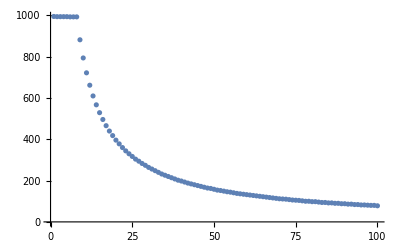

```mathematica
ListPlot[iterInter2List]
```

Plot of theoretical number of cars passed without an intersection:

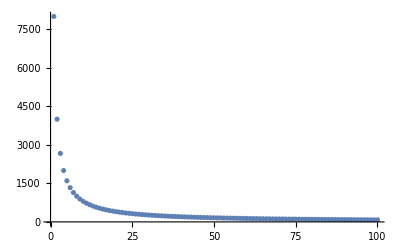

```mathematica
ListPlot[4000/Range[100]*2,PlotRange->Full]
```

The efficiency graph I plotted after dividing actual/theoretical:

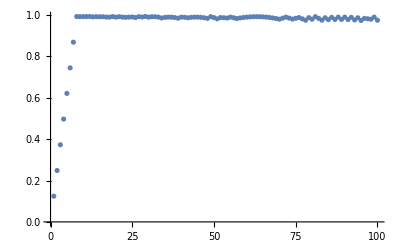

```mathematica
ListPlot[MapThread[Divide,{iterInter2List,4000/Range[100]*2}],PlotRange->Full]
```

### Conclusion

#### There are many steps that could be taken to further this project. In the future, I want to experiment with more types of intersections. Since I only concentrated on four-way intersections, I think it would be very interesting to look into intersections such as roundabouts and various n way intersections. Also, although I am aware that it would be very difficult, I want to figure out how the traffic would be with acceleration.